## Common elements

References:
[MSc] F.Hekhorn, “Sub-leading Terms in Heavy Quark Soft Gluon Resummation”, MSc Thesis Universität Tübingen, Germany, 2015.
[Bonc] R. Bonciani, S. Catani, M. L. Mangano, and P. Nason, “NLL resummation of the heavy quark hadroproduction cross-section,” Nucl.Phys. B529 (1998) 424–450, arXiv:hep-ph/9801375 [hep-ph].
[InvMelTh] https://en.wikipedia.org/wiki/Mellin_inversion_theorem
[MP] S. Catani, M. L. Mangano, P. Nason, and L. Trentadue, “The resummation of soft gluons in hadronic collisions,” Nuclear Physics B 478 no. 1–2, (1996) 273 – 310.

```mathematica
(* load packages *)
AppendTo[$Path, ToFileName[{$HomeDirectory,"Physik/PhD/MMa"}]];
Get["MellinTrafoLogCoeffs.m"]
Get["SudakovFactor.m"]
Get["NumericMellinTrafo.m"]
Needs["HEPMath`LHAPDF`"]
(*Get["PdfUtils.m"]*)
Get["zPlot.m"]
Needs["PlotLegends`"]
```

ν::shdw: Symbol "\[Nu]" appears in multiple contexts {"SudakovFactor`", "Global`"}; definitions in context "SudakovFactor`" may shadow or be shadowed by other definitions.

```mathematica
(* give concrete parameters *)
CFCASub = {CF -> 4/3, CA -> 3};
(* @param mQ override default mass *)
(* @param αμ override default running coupling from PDF *)
Options[toN] = {"channel" -> "γg","Q" -> "c","pdfParams"-> {"cteq66",0}, "mQ"-> -1, "αμ"-> -1};
toN[opts:OptionsPattern[]] := Module[{Q,ch,cαμ,r,l,p},
Q=OptionValue["Q"];
ch=OptionValue["channel"];
r=SudakovFactor`getRules[ch];
(* params related to quark *)
l = {
nl-> Switch[Q,"t",5,"b",4,"c",3,_,Throw["unknown quark"]] ,(* number light flaours *)
eQ-> Switch[Q,"t",2/3,"b",-1/3,"c",2/3,_,Throw["unknown quark"]] ,(* electric charge *)
mQ-> If[OptionValue["mQ"] >0,OptionValue["mQ"],Switch[Q,"t",173.070,"b",4.180,"c",1.5(*1.275*),_,Throw["unknown quark"]]], (* [GeV] *)
μ-> mQ (* [GeV] *)
};
(* params related to PDF *)
cαμ=OptionValue["αμ"];
p={αμ-> If[NumericQ[cαμ]&& cαμ≤ 0,
Evaluate@Module[{pdfId,α},
pdfId=LHAPDFOpen@@OptionValue["pdfParams"];
α=LHAPDFAlphaS[pdfId,μ//.l];
LHAPDFClose[pdfId];
α
],
cαμ]};
(* join all *)
Join[r,CFCASub,l,p,{lnRScale4->lnScale4,lnFScale4 ->lnScale4,lnScale4-> Log[μ^2/(4*mQ^2)]}]
];
nLandau =Exp[1/(2αμ*b0)];
```

```mathematica
(* transformations *)
ρ2β[ρ_]=Sqrt[1-ρ];
β2ρ[β_]=1-β^2;
ρ2η[ρ_]=1/ρ-1;
η2ρ[η_] = 1/(1+η);
β2χ[β_]=(1-β)/(1+β);
χ2β[χ_]=(1-χ)/(1+χ);
s2ρ[s_]=4*mQ/s;
vars2ρ[e_] :=e//. {β->ρ2β@ρ,η->ρ2η@ρ,χ->β2χ@ρ2β@ρ};
```

```mathematica
(* compute common resummation functions *)
Do[commonG[n] = getG[n],{n,1}]
```

```mathematica
(* build resummation factor *)
ΔLL = Exp[lnN * commonG[1][αμ*b0*lnN]];
```

```mathematica
(* used colors *)
Table[Graphics[{c,Disk[]},ImageSize-> 50],{c,ColorData[3,"ColorList"]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Born cross section

```mathematica
(* Born cross sections of unpol. photoproduction *)
Born = π/4 ρ(-(3-β^4)Log[χ]+2β^3-4β);
Module[{a,mlnχ},
a = {0.9991,−0.4828,0.2477,−0.0712};
mlnχ[u_,v_]=n↦Beta[n+u,v/2+1](PolyGamma[n+u+v/2+1]-PolyGamma[n+u])+2*Sum[a[[j]]*Beta[n+u,(v+j)/2+1],{j,Length@a}];
BornN = n↦Evaluate[π/4*(-4Beta[n+1,3/2]+2Beta[n+1,5/2]+3*mlnχ[1,0][n]-mlnχ[1,4][n])];
]
```

```mathematica
(* deduce series of Born in β *)
(*Series[-Log[β2χ@β],{β,0,11}]
Table[2(1/(2k-1)),{k,6}]
Series[-(3-β^4)Log[β2χ@β],{β,0,11}]
{6,2}~Join~Table[2(3/(2k-1)-1/(2k-5)),{k,3,6}]
{2,2,-4-4/5}~Join~Table[2(3/(2k-1)-3/(2k-3)-1/(2k-5)+1/(2k-7)),{k,4,8}]*)
BornβSerCoeff[1] =1;
BornβSerCoeff[2] =1;
BornβSerCoeff[3] =-12/5;
BornβSerCoeff[k_Integer] := (3/(2k-1)-3/(2k-3)-1/(2k-5)+1/(2k-7))/;k>3;
(* check *)
Series[2/π*(vars2ρ@Born/.{ρ-> β2ρ@β}),{β,0,21}]
Table[BornβSerCoeff@k,{k,11}]
(* the coefficients sum up to 0 *)
(* maybe this results hold more generally for all kind of partonic Born cross sections? at least it does for hadro-quark *)
BornβSerCoeff[1]+BornβSerCoeff[2]+BornβSerCoeff[3]+Sum[(3/(2k-1)-3/(2k-3)-1/(2k-5)+1/(2k-7)),{k,4,∞}]
(* numeric check *)
Table[N@Total[CoefficientList[Normal@Series[(Born//.{χ-> β2χ@β,ρ-> β2ρ@β}),{β,0,2*k-1}],β]],{k,{1,2,3,5,10,20,50,100,1000}}]
```

β+β^3-(12 β^5)/5+(52 β^7)/105+(4 β^9)/105-(4 β^11)/1155-(92 β^13)/9009-(68 β^15)/6435-(116 β^17)/12155-(524 β^19)/62985-(244 β^21)/33915+O[β]^22

{1,1,-12/5,52/105,4/105,-4/1155,-92/9009,-68/6435,-116/12155,-524/62985,-244/33915}

0

{1.5708,3.14159,-0.628319,0.20944,0.143301,0.0759506,0.0310652,0.015625,0.00157001}

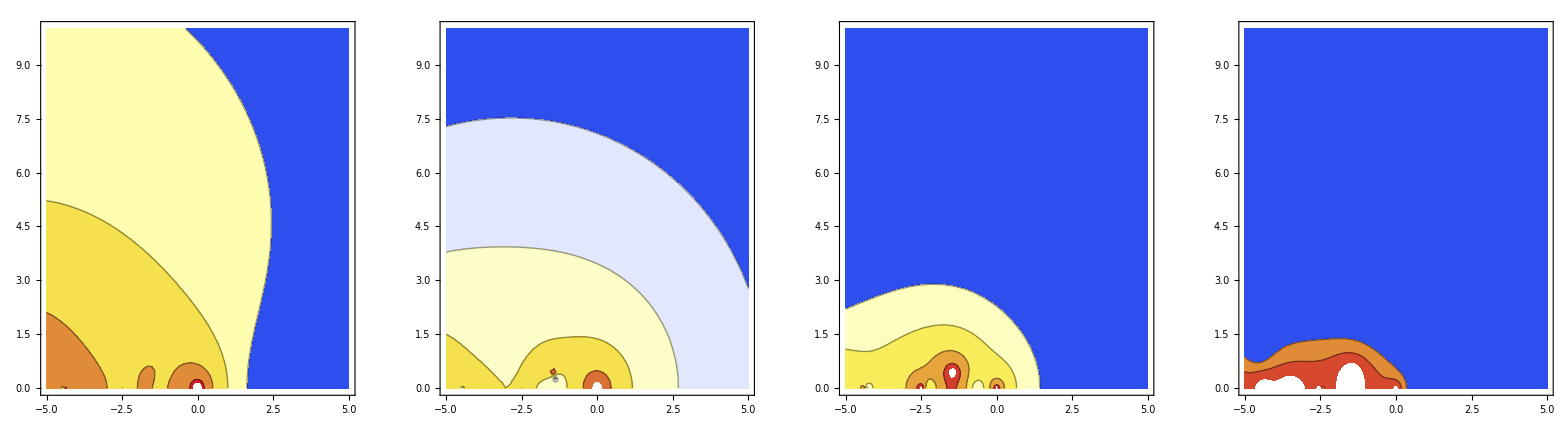

```mathematica
(* check convergence in N-space: *)
Module[{orders,BornMaxSer,BornSers,BornSerβList,BornSerNs,m},
orders = {1,3,5,9};
(* compute series *)
BornMaxSer=Normal@Series[(Born//.{χ-> β2χ@β,ρ-> β2ρ@β}),{β,0,Max@orders}];
BornSers = Table[Normal@Series[BornMaxSer,{β,0,v}],{v,orders}];
(* transform to N *)
BornSerβList=(s↦CoefficientList[s,β])/@BornSers;
BornSerNs=(l↦(n↦Evaluate[l//.{m-> n}]))/@((l↦Total[MapIndexed[Function[{c,ind},c*Beta[m,(First@ind-1)/2+1]],l]])/@BornSerβList);
GraphicsRow[(f↦ContourPlot[Log[Abs[(BornN[n]-f[n])/BornN[n]]//.{n-> re + I im}],{re,-5,5},{im,0,10},ColorFunction->"TemperatureMap",Contours-> {-2,-1,0,1,2,3}])/@BornSerNs]
]
```

## Compare re-expansion to full resummation

Question (Q): how does the reexpanion of the Sudakov-exponent behave? Reexpansion refers to the exponent (i.e. exp ~ 1+O(lnN)). Does it converge in (any sense) to the full resummation?
Conjecture (C): No. Long Answer see [MSc]: “This is probably the reason why the re-expansion of the resummed expression does not converge to the fully resummed expression because near threshold the region N → ∞ is relevant, but it is obviously not in the region of convergence. So how is it possible to match the re-expansion and fixed-order calculations as said above in section 3.2.1? It is probably possible because they rely on the same assumption: α s (μ 2 ) is a small number. If α s is not a good expansion parameter (as it did not catch the relevant region), is there any other? Unfortunately not, because there is always a structure with ln ln x, that limits the convergence.” Can we precise this statement any further?

As a first step I always use the “threshold-resummation”, i.e. I use only a single Beta-function in resummation and NOT the full Born cross section. In a second step, I look on what would change by taking the full Born

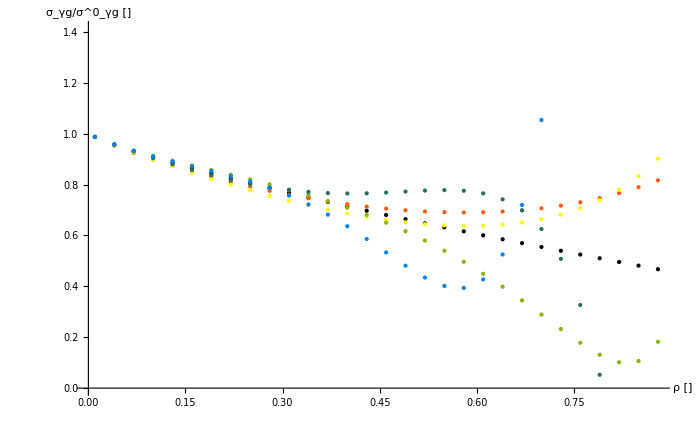

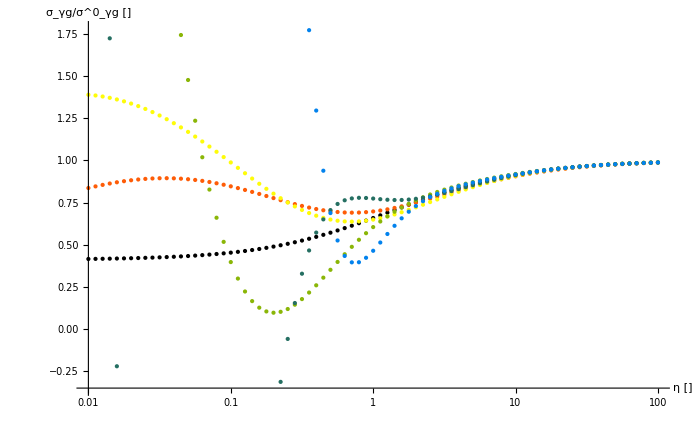

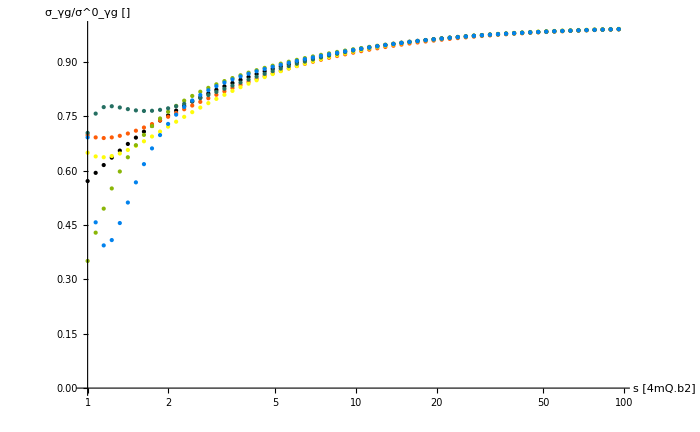

```mathematica
(*
 overall picture:
first element refers to full resummation
plot different variables: ρ,η,s
*)
Module[{v,orders,
fullN,serΔLLMax,serΔLLs,serNs,fullρ,serρs,
computeOnGrid,
ρs,lρs,toρPlot,
ηs,lηs,toηPlot,
ss,lss,tosPlot
},
v=1; (* σ ~ β^v <-> Beta[n,v/2+1] *)
orders={2,3,5,7,10};(* At which orders should the expansion be taken? *)
(* get series *)
serΔLLMax = Normal@Series[ΔLL,{lnN,0,Max@orders}];
serΔLLs =Table[Normal@Series[serΔLLMax,{lnN,0,o}],{o,orders}];
(* build functions *)
fullN = n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]})];
serNs =(s↦ (n↦Evaluate[Beta[n,v/2+1]*(s/.{lnN -> Log[n+1]})]))/@serΔLLs;
(*Print@fullN;Print@serN;*)
(* compute inverse *)
fullρ = getInvMellinTrafo[fullN//.toN[]];
serρs=(f↦getInvMellinTrafo[f//.toN[]])/@serNs;
(* compute values on grid *)
(* @param xs list to iterate *)
(* @param t transformation function applies to each element in list (to transform to ρ) *)
computeOnGrid[xs_List,t_Function] := Join[
{Parallelize@Table[fullρ[t@x],{x,xs}]},
(fρ↦Parallelize@Table[fρ[t@x],{x,xs}])/@serρs
];
(* equidistant ρ points; equivalent to alter mQ equidistant *)
ρs=Table[j,{j,.01,.9,.03}];
lρs=computeOnGrid[ρs,ρ↦ρ];
toρPlot[l_]:=Transpose[{ρs,l}];
(*Print@lρs;*)
Print@Show[ListPlot[(l↦toρPlot@Re@l)/@lρs,AxesLabel-> {"ρ []","σ_γg/σ^0_γg []"},PlotStyle->ColorData[3,"ColorList"]],ImageSize-> 700];
(* logarithmic η points *)
ηs = Table[10^(j),{j,-2,2,.05}];
lρs=computeOnGrid[ηs,η↦η2ρ@η];
toηPlot[l_]:=Transpose[{ηs,l}];
(*Print@lFullηs;Print@lSerηs;*)
Print@Show[ListLogLinearPlot[(l↦toηPlot@Re@l)/@lρs,AxesLabel-> {"η []","σ_γg/σ^0_γg []"},PlotStyle->ColorData[3,"ColorList"]],ImageSize-> 700];
(* equidistant s points *)
ss = Table[10^j,{j,0,2,.03}];
lss=computeOnGrid[ss,s↦s2ρ[(s*4mQ^2)]//.toN[]];
tosPlot[l_]:=Transpose[{ss,l}];
(*Print@lFullss;Print@lSerss;*)
Print@Show[ListLogLinearPlot[(l↦tosPlot@Re@l)/@lss,AxesLabel-> {"s [4mQ.b2]","σ_γg/σ^0_γg []"},PlotStyle->ColorData[3,"ColorList"]],ImageSize-> 700];
]
```

### Case 1: Threshold limit

First let’s take a look at the threshold region: I conjecture really bad behaviour here, cause any power of ln(N) will introduce a power of ln(β) as I proved in [MSc]

#### Lemma: compare analytic expansion via d_(w,j)(v) to numeric inversion

First let’s check how good the deduced coefficients describe the threshold behavior, so I compare my coefficients d_(w,j)(v) to the numeric inversion of ln^w(N)
Q: Are the coefficients d_(w,j)(v) sufficient near threshold?

```mathematica
(* @param v σ ~ β^v <-> Beta[n,v/2+1] *)
(* @param orders At which orders should the expansion be checked? *)
checkDToNumericInv[v_,orders_List]:=Module[{
ηs,numericFNs,lNumerics,fβs, lAnalytics,lErrs
},
ηs = Table[10^j,{j,-4,0,.03}];
(* compute numeric inversion *)
numericFNs = (o↦(n↦Beta[n,v/2+1]*Log[n+1]^o))/@orders;
lNumerics = (fN↦Parallelize@Table[getInvMellinTrafo[fN][η2ρ@η],{η,ηs}])/@numericFNs;
(* compute analytic inversion *)
fβs=(w↦(β↦β^v*(-1)^w*Sum[getD[w,j,v]*Log[β]^(w-j),{j,0,w}]))/@orders;
(* plot functions *)
(*Print@GraphicsRow[{
ListLogLinearPlot[(l↦Transpose[{ηs,l}])/@lNumerics,PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","σ_γg/σ^0_γg []"}],
LogLinearPlot[Evaluate[(f↦f[ρ2β@η2ρ@η])/@fβs],{η,Min@ηs,Max@ηs},PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","σ_γg/σ^0_γg []"}]
},ImageSize->800 ];*)
(* compute analytic at ηs *)
lAnalytics=(f↦Table[f[ρ2β@η2ρ@η],{η,ηs}])/@fβs;
(* compute relative error *)
lErrs = (Re@lNumerics-Re@lAnalytics)/Re@lNumerics;
(* plot errors *)
ListLogLogPlot[(l↦Transpose[{ηs,Abs@l}])/@lErrs,PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","rel. error []"}]
]
```

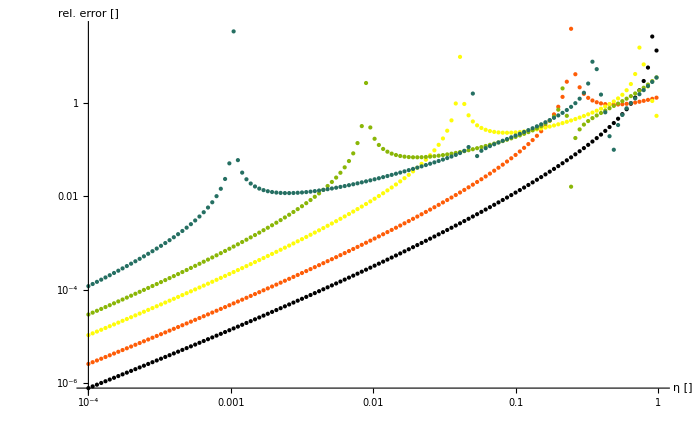

```mathematica
Show[checkDToNumericInv[1,{2,3,5,7,10}] ,ImageSize-> 700]
```

Answer (A): Yes, the coefficients are sufficient;
- the higher the power of ln^w(N), the later is the convergence, but nevertheless they converge
- the peaks to ∞ in the error-plot correspond to zeros of numeric inversion, that doesn’t get matched exactly by analytic inversion
- the peaks to 0 in the error-plot correspond to intersection between, analytic and numeric inversion

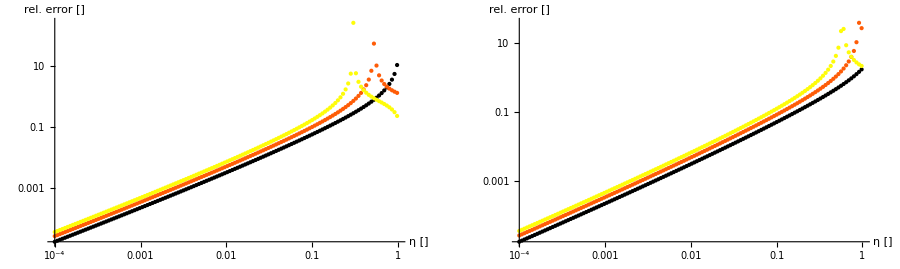

```mathematica
GraphicsRow[{
checkDToNumericInv[3,{2,3,4}],
checkDToNumericInv[5,{2,3,4}]
},ImageSize-> 900]
```

A: this is independent of v;
- propably: the higher v, the faster the convergence

#### Full resummation

The full resummation [is] seems constant > 0 near threshold

```mathematica
(* plot full resummation near threshold *)
(* @param v σ ~ β^v <-> Beta[n,v/2+1]  *)
Options[plotFullAtThreshLimit]={"toN"-> {}};
plotFullAtThreshLimit[v_,opts:OptionsPattern[]]:=Module[{f,ηs,l},
ηs = Table[10^j,{j,-7,0,.1}];
f=n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]})//.toN[FilterRules[OptionValue["toN"], Options[toN]]]];
l = Parallelize@Table[getInvMellinTrafo[f][η2ρ@η],{η,ηs}];
ListLogLinearPlot[Transpose[{ηs,l}],AxesLabel-> {"η []","σ_γg/σ^0_γg []"}]
];
```

This seems to be independet of v

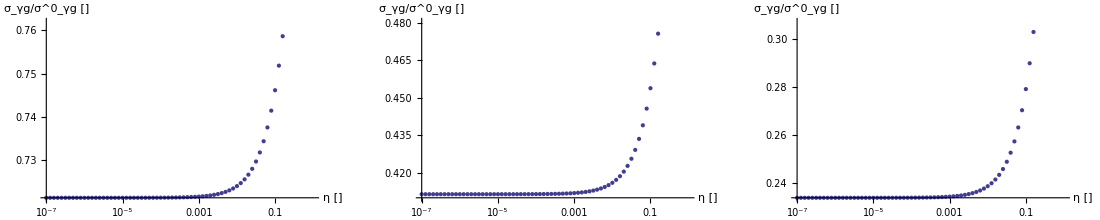

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[0],
plotFullAtThreshLimit[1],
plotFullAtThreshLimit[2]
},ImageSize-> 1100]
```

#### Problems with full resummation

BUT: I would have expected this threshold value to be independent of channel, as N→∞ beats everything, esp. exp(2x) or exp(4x) as the difference between γg and gg8 is;
it isn’t

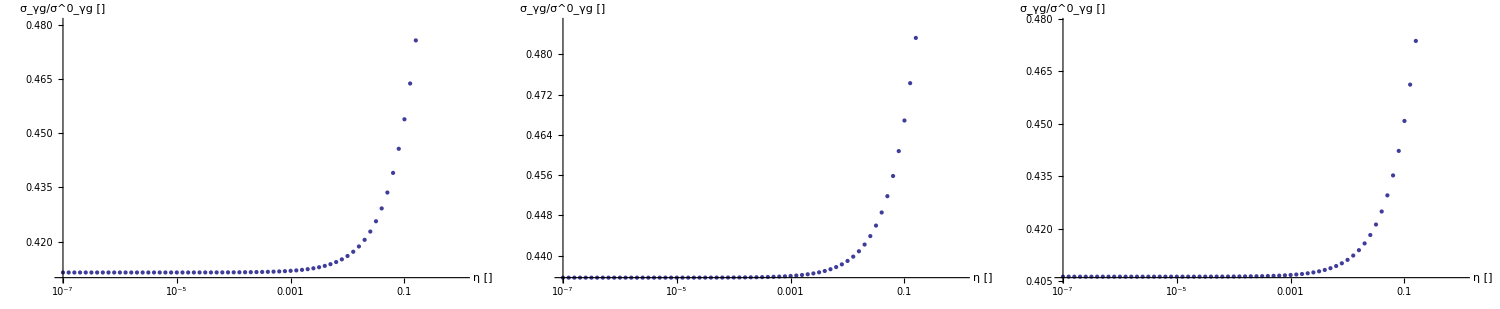

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "γg"}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "gg8"}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "qqbar8"}]
},ImageSize->1500,Spacings-> 0]
```

I also expected this threshold value to be independent of quark, as N→∞ beats everything, esp. exp(.36*x) or exp(.15*x) as the difference the quarks/the running coupling,
but it isn’t

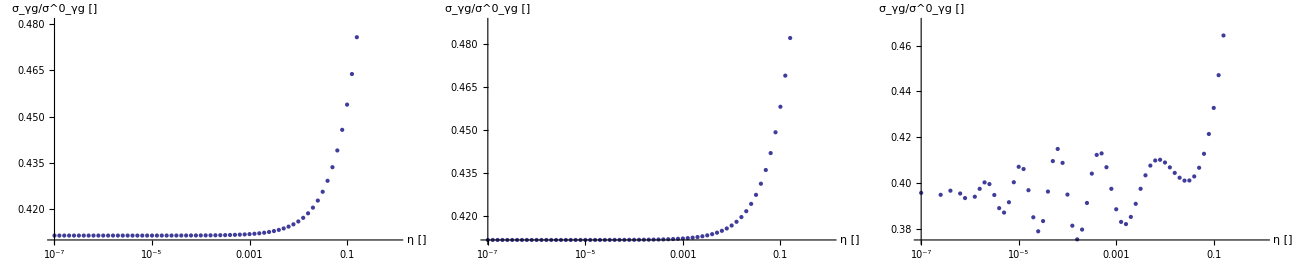

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c"}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "b"}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "t"}]
},ImageSize-> 1300,Spacings-> 0]
```

And, even worse, we seen some wild oscillations occuring before a constant is approached.
This problem rises from α beeing TOO SMALL (!) as can be seen in the following plot:
(NB: mQ→∞ ⇔ αμ→0)

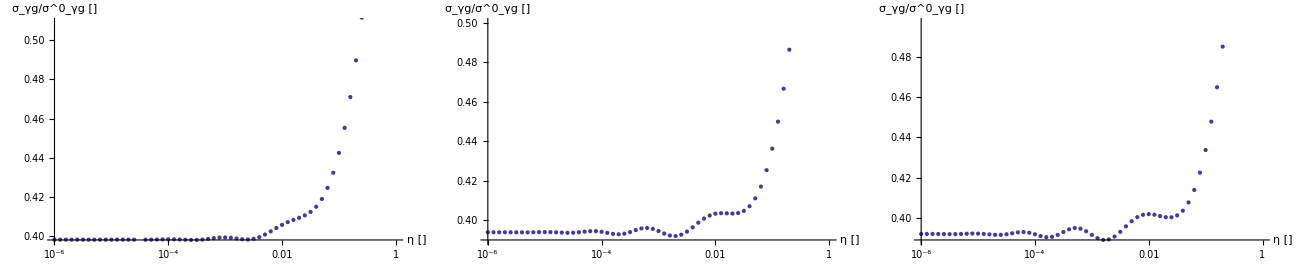

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","mQ"-> 50}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","mQ"-> 100}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","mQ"-> 130}]
},ImageSize->1300,Spacings-> 0]
```

of course it also depends on b0, as b0 and α are appearing almost everywhere together: λ=α b0 ln(N) (b0 can be modified by the detected quark b0(charrn) > b0(top))

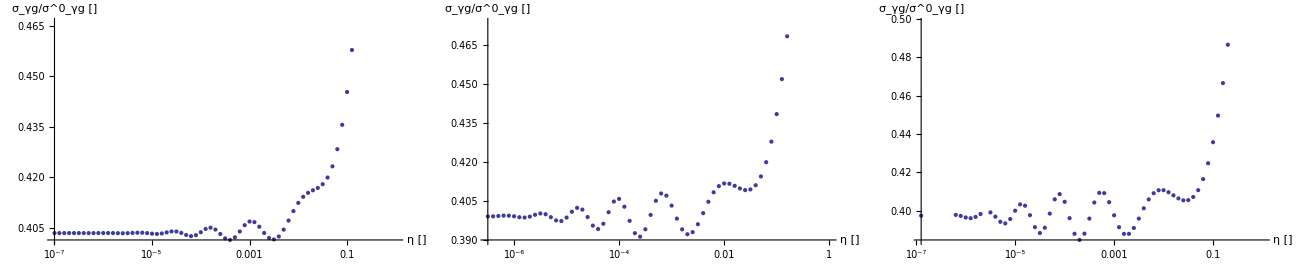

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "t","mQ"-> 50}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "t","mQ"-> 100}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "t","mQ"-> 130}]
},ImageSize->1300,Spacings-> 0]
```

Alright lets track this oscillating-problem a bit: it depends strongly on v as can be seen here:

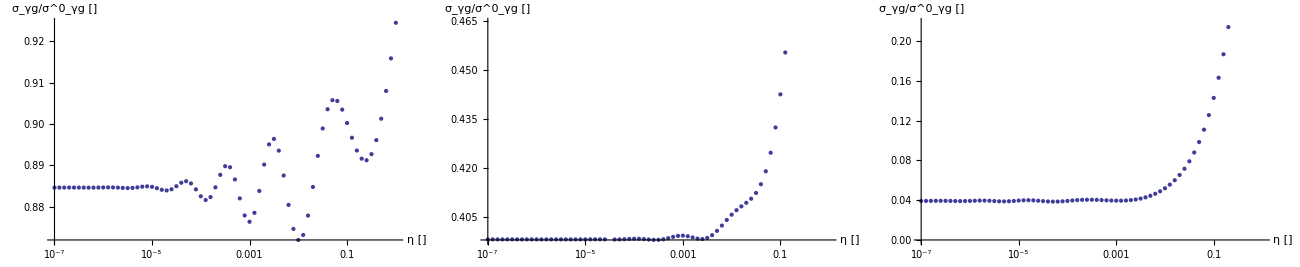

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[0,"toN"-> {"Q"-> "c","αμ"-> .15}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","αμ"-> .13}],
plotFullAtThreshLimit[2,"toN"-> {"Q"-> "c","αμ"-> .07}]
},ImageSize->1300,Spacings-> 0]
```

It depends on the channel

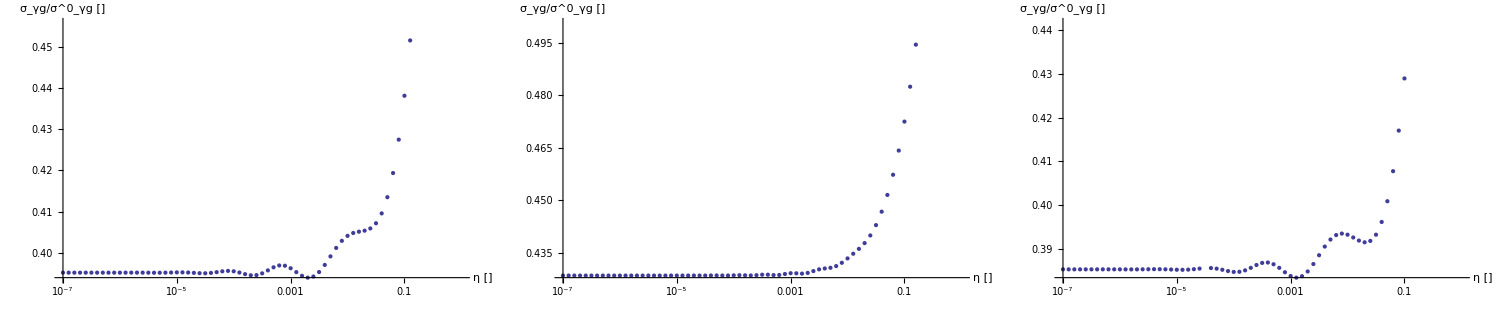

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "γg","αμ"-> .12}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "gg8","αμ"-> .12}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "qqbar8","αμ"-> .12}]
},ImageSize->1500,Spacings-> 0]
```

Wild guessing: what form has the exact inversion to take to make such oscillations?

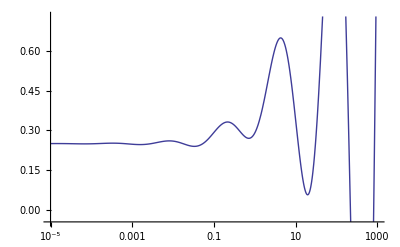

```mathematica
LogLinearPlot[.5-.25η2ρ[η]+.1Sin[2Log@η-1]*Exp[.5Log@η],{η,1*^-5,1*^3}]
```

Alrght:
- I don’t know, why these oscillations are occuring, and why they are appearing for small α
- this oscillation has already be found in [Bonc]
- nevertheless is seems BEYOND these oscillations (i.e. for even smaller η (smaller then in [Bonc])) the function still seems to approach a constant, but this region is numerically instable as well

Let’s see if we can find out a bit more about the threshold value (the constant value I’m suggesting)
Can we specify the dependencies a bit better?

```mathematica
(* plot full resummation for different running couplings αμ or equivalently mQ *)
(* Remember: α,μ ~ 1/ln(mQ) i.e. mQ->0⇒αμ->∞ and mQ->∞⇒αμ->0 *)
(* @param v σ ~ β^v <-> Beta[n,v/2+1]  *)
(* @param ρ ρ-point at which value is calculated  *)
getFullOnRunningPlots[v_,ρ_]:=Module[{f,ms,αμs,lms,lαμs},
f=n↦Beta[n,v/2+1]*(ΔLL//.{lnN -> Log[n+1]});
ms = Table[10^j,{j,0.2,2.5,.1}];
lms = Table[getInvMellinTrafo[n↦Evaluate[f[n]//.toN["mQ"-> m]]][1],{m,ms}];
αμs=Table[j,{j,.15,.8,.03}];
lαμs =Table[getInvMellinTrafo[n↦Evaluate[f[n]//.toN["αμ"-> cαμ]]][ρ],{cαμ,αμs}];
GraphicsRow[{
ListLogLinearPlot[Transpose[{ms,lms}],AxesLabel-> {"m [GeV]","σ_γg/σ^0_γg []"}],
ListPlot[Transpose[{αμs,lαμs}],AxesLabel-> {"αμ []","σ_γg/σ^0_γg []"}]
}]
]
```

We always use real threshold i.e. ρ=1 and we get the following picture:

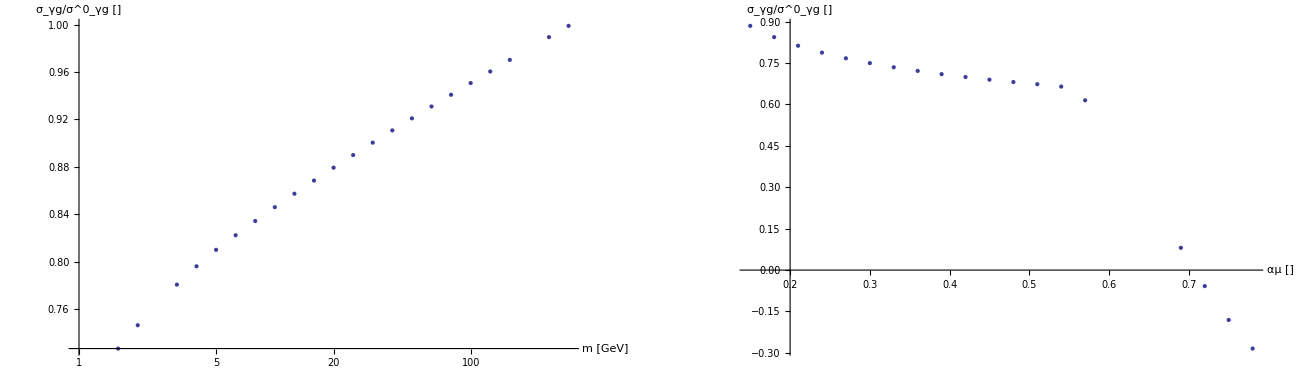

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2158.06  + 1351.24\ ⅈ
 and 1202.38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 17423.7  + 2537.64\ ⅈ
 and 8183.07 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 76617.3  + 86151.2\ ⅈ
 and 52336.4 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

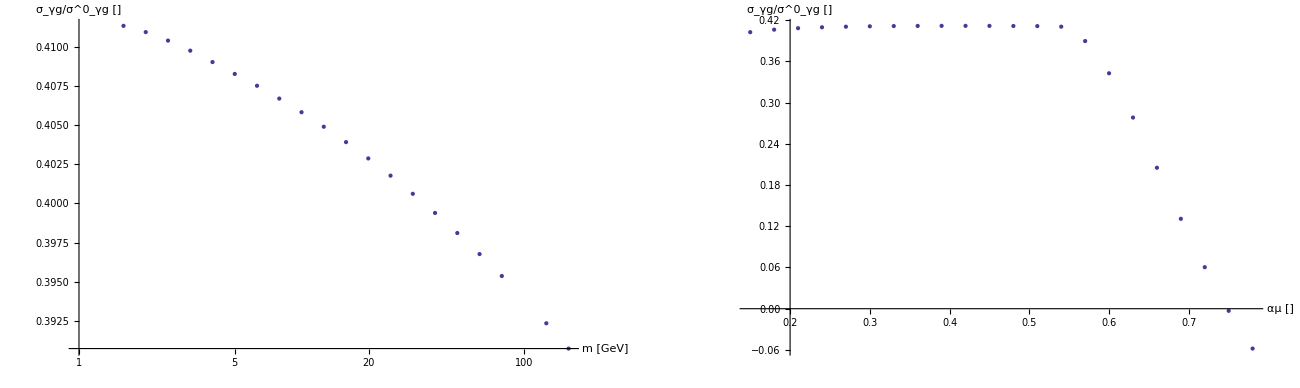

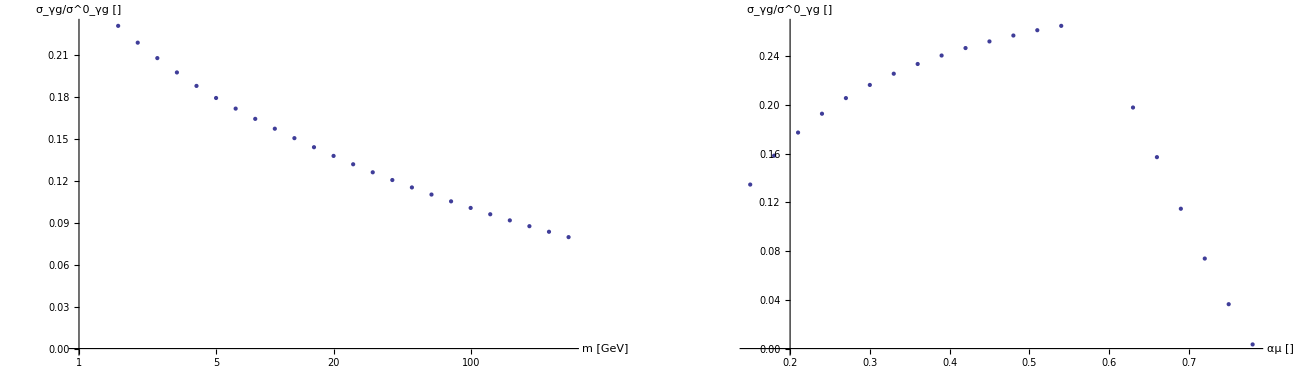

```mathematica
Show[getFullOnRunningPlots[0,1],ImageSize-> 1300]
Show[getFullOnRunningPlots[1,1],ImageSize-> 1300]
Show[getFullOnRunningPlots[2,1],ImageSize-> 1300]
```

And this is even more supprising:
- the shapes for v=1 and v=2 are kind of similar, but v=0 (would correspond to leading Coulomb term) has a different shape
- furthermore we find σ(σ=1) < 0 for αμ getting to large. We would expect problems for αμ getting to large, but does this hold at threshold? I would have expected problems comming to threshold as αμ increases, but at threshold?

#### Reexpansion

The analytic inversion in contrast is f(β→0)→0 as β^v is always stronger then ln(β)^w

```mathematica
Limit[β^v*Log[β],β-> 0,Assumptions-> {v>0}]
```

0

Furthermore the coefficients are wildy oscillating near threshold

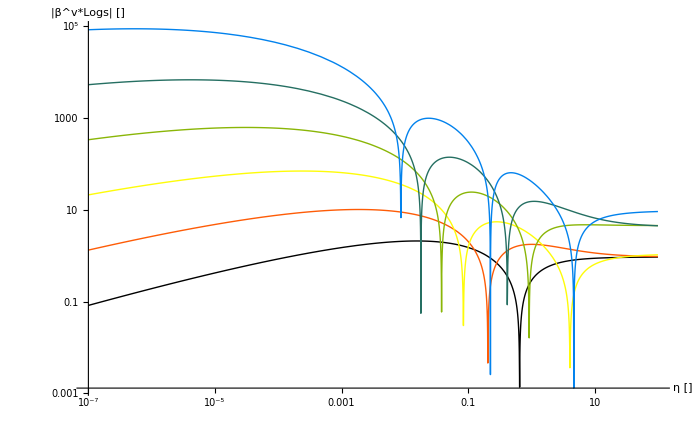

```mathematica
Module[{v,orders,fβs},
v = 1;(* σ ~ β^v <-> Beta[n,v/2+1] *)
orders={2,3,4,5,6,7};
(* compute analytic inversion *)
fβs=(w↦(β↦β^v*(-1)^w*Sum[getD[w,j,v]*Log[β]^(w-j),{j,0,w}]))/@orders;
Show[LogLogPlot[Evaluate[(f↦Abs@f[ρ2β@η2ρ@η])/@fβs],{η,1*^-7,1*^2},PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","|β^v*Logs| []"}],ImageSize-> 700]
]
```

Problems with the coefficients:
- the higher w, the more real zeros on η in [0,1] exist
- the higher w, the smaller the smallest zero gets
- the higher w, the later is the convergence f(η→0)→0
- the higher w, the higher is e.g. f(η=1e-5)

A: the reexpansion will NOT be related to the full resummation in the threshold limit

#### [probably wrong] don’t use Beta-function in resummation?

- What would be if we just compute the inverse of the raw Sudakov-exponent?
- well, probably this will NOT work, as we need some regularising function - either Beta-function or N^(-k)
- cause “If ϕ(s) is analytic in the strip a < Re(s) < b, and if it tends to zero uniformly as Im(s)→±∞ for any real value c between a and b, with its integral along such a line converging absolutely, then [the inversion exists]”[InvMelTh] and this is clearly not the case as |ln(N)| >= ln(|N|); i.e. the expression grows in all directions
- nevertheless can Mathematica compute the inverse, but this is probably due to the contour-deforming-trick of [MP]; this trick is (I think) numerically needed, but we’re not allowed to be mathematical dependent on it

{1+(lnN^2 αμ ν SudakovFactor`Private`Ak[1])/π,1+(lnN^2 αμ ν SudakovFactor`Private`Ak[1])/π+(2 b0 lnN^3 αμ^2 ν SudakovFactor`Private`Ak[1])/(3 π),1+(lnN^2 αμ ν SudakovFactor`Private`Ak[1])/π+(2 b0 lnN^3 αμ^2 ν SudakovFactor`Private`Ak[1])/(3 π)+(lnN^4 (4 b0^2 π αμ^3 ν SudakovFactor`Private`Ak[1]+3 αμ^2 ν^2 (SudakovFactor`Private`Ak[1])^2))/(6 π^2)}

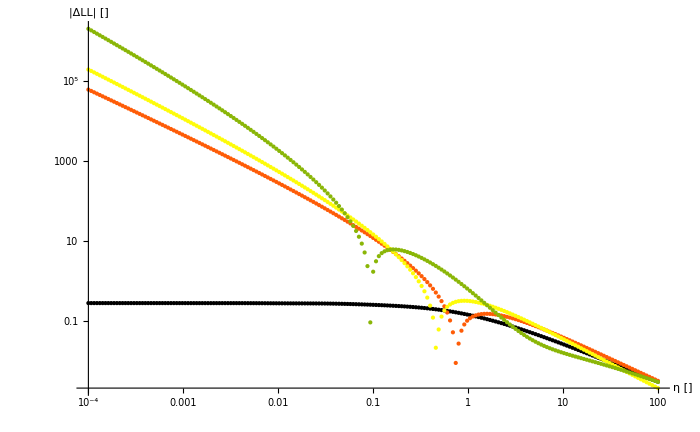

```mathematica
Module[{orders,f,gMaxOrder,gs,gNs,ηs,lf,lNumericgN,analyticgNs,lnN2ρ,ind2w},
orders={2,3,4};
(* build functions *)
f =n↦Evaluate[(ΔLL//.{lnN -> Log[n+1]})//.toN[]];
gMaxOrder=Normal@Series[ΔLL,{lnN,0,Max@orders}];
gs = Table[Normal@Series[gMaxOrder,{lnN,0,w}],{w,orders}];
Print@gs;
gNs=(g↦(n↦Evaluate[g//.{lnN-> Log[n+1]}//.toN[]]))/@gs;
(* plot *)
(*Print[{zPlotReIm[f]}~Join~Table[zPlotReIm@gN,{gN,gNs}]];*)
(* compute on grid *)
ηs=Table[10^j,{j,-4,2,.03}];
lf=Parallelize@Table[getInvMellinTrafo[f][η2ρ@η],{η,ηs}];
lNumericgN  = (gN↦Parallelize@Table[getInvMellinTrafo[gN][η2ρ@η],{η,ηs}])/@gNs;
(*lnN2ρ[w_]=Limit[D[Exp[(k-1)Log@Log[1/ρ]-Log[Gamma[ρ]]],{k,w}],k-> 0];
ind2w[ind_]:=First@ind-1;
analyticgNs=(g↦MapIndexed[Function[{c,ind},c*lnN2ρ[ind2w@ind]],CoefficientList[g,{lnN}]])/@gs;
Print@analyticgNs;*)
(*Print@ListLogLinearPlot[Transpose[{ηs,l}]];*)
Print@Show[ListLogLogPlot[Evaluate[Abs@({Transpose[{ηs,lf}]}~Join~((l↦Transpose[{ηs,l}])/@lNumericgN))],PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","|ΔLL| []"}],ImageSize-> 700];
(*LogLogPlot[Evaluate[(g↦Abs[g/.{ρ-> η2ρ@η}//.toN[]])/@analyticgNs],{η,1*^-4,1*^2}]*)
]
```

I don’t know how such functions can be inverted ...

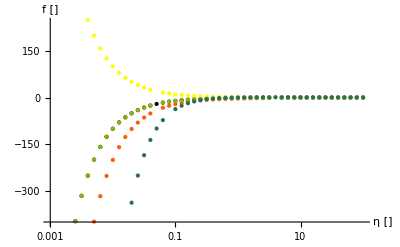

```mathematica
Module[{fNs,ηs,ls},
fNs={n↦1+Log[n],n↦2*Log@n,n↦1-Log[n],n↦Log[n],n↦1+Log[n]^2};
ηs=Table[10^j,{j,-3,2,.1}];
ls=(f↦Parallelize@Table[getInvMellinTrafo[f][η2ρ@η],{η,ηs}])/@fNs;
Print@ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,l}])/@ls],PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","f []"}];
]
```

[MP] gave the inversion of ln^w(N)/N^k but this is only valid for Re(k) >0
and yes if we plug k=0 into their formula, we don’t get the same as above

(Log[1/ρ]^(-1+k) Log[Log[1/ρ]]^2)/Gamma[ρ]

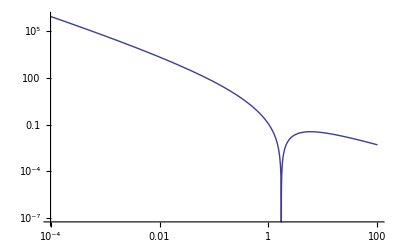

```mathematica
D[Exp[(k-1)Log@Log[1/ρ]-Log[Gamma[ρ]]],{k,2}]
LogLogPlot[Abs[Limit[D[Exp[(k-1)Log@Log[1/ρ]-Log[Gamma[ρ]]],{k,2}],k-> 0]]/.{ρ-> η2ρ@η},{η,1*^-4,1*^2}]
```

as already said is ln^w(N) growing in all directions

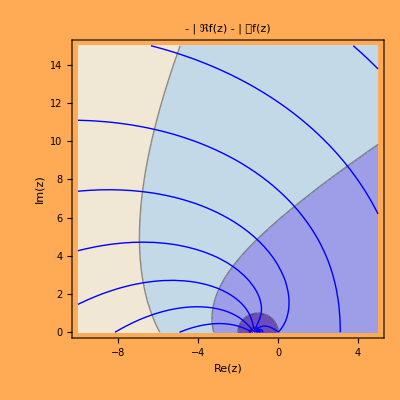

```mathematica
zPlotReIm[n↦Log[n+1]^2,"ymin"-> 0,"xmin"-> -10,"ymax"-> 15]
```

### Case 2: High-energy limit

NB: this section is really theoretical, as I can NOT say, whether resummation is physically valid at all in this limit; so for the moment let’s forget the physics and compare the functions in a mathematical point of view
NB: this limit is numerically unstable[MSc], so I have to guess a bit, and this is why MMa is complainig about “suspect highly oscillatory integrand”; yes, it is
NB: unfortunaly I first forgot the shift to N+1, and it turns out this changed the picture completly - so yes the shift is important (and from this, I think, we can conclude HE-Limit ⇔ ρ→0⇔N→1(0?))

```mathematica
(* @param v σ ~ β^v <-> Beta[n,v/2+1] *)
(* @param orders At which orders should the expansion be checked? *)
getDiffHELimit[v_,orders_]:=Module[{
fullN,serΔLLMax,serΔLLs,serNs,fullρ,serρs,
ss,lFull,lSer,tosPlot
},
(* get series *)
serΔLLMax = Normal@Series[ΔLL,{lnN,0,Max@orders}];
serΔLLs =Table[Normal@Series[serΔLLMax,{lnN,0,o}],{o,orders}];
(* build functions *)
fullN = n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]})];
serNs =(s↦ (n↦Evaluate[Beta[n,v/2+1]*(s/.{lnN -> Log[n+1]})]))/@serΔLLs;
(* compute inverse *)
fullρ = getInvMellinTrafo[fullN//.toN[]];
serρs=(f↦getInvMellinTrafo[f//.toN[]])/@serNs;
(* compute values on grid *)
ss = Table[10^j,{j,1,3,.03}];
lFull = Parallelize@Table[fullρ[s2ρ[s*4mQ^2]//.toN[]],{s,ss}];
lSer = (fρ↦Parallelize@Table[fρ[s2ρ[s*4mQ^2]//.toN[]],{s,ss}])/@serρs;
(* Plot *)
tosPlot[l_]:=Transpose[{ss,l}];
(*Print@Show[ListPlot[tosPlot@Re@lFull,AxesLabel-> {"s [4mQ.b2]","σ_γg/σ^0_γg []"}],ImageSize-> 700];*)
ListLogLogPlot[(l↦tosPlot@Abs[(Re@l-Re@lFull)/Re@lFull])/@lSer,AxesLabel-> {"s [4mQ.b2]","rel. error []"},PlotStyle->ColorData[3,"ColorList"]]
]
```

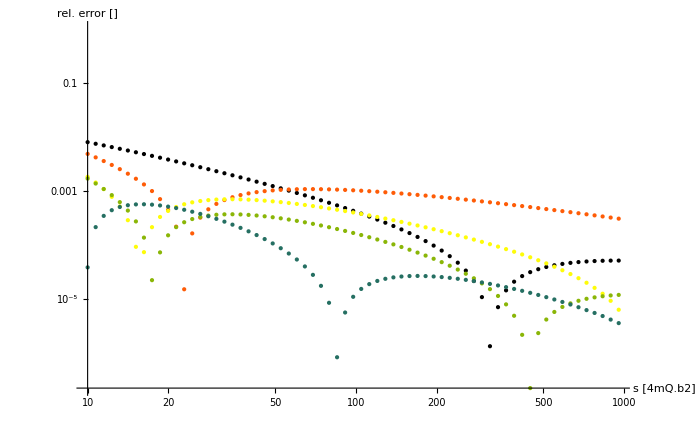

```mathematica
Show[getDiffHELimit[1,{2,3,5,7,10}],ImageSize-> 700]
```

A: Yes, the reexpansion will converge towards the full resummation
- it oscillates around full resummation
- the higher the expansion, the smaller gets the amplitude
- the higher the expansion, the faster gets the frequency

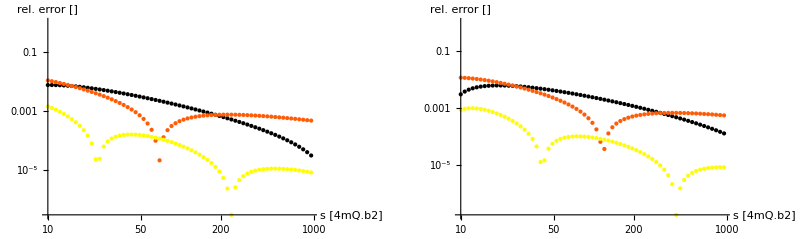

```mathematica
GraphicsRow[{
getDiffHELimit[3,{2,3,10}],
getDiffHELimit[5,{2,3,10}]
},ImageSize-> 800]
```

A: this is independent of v
A: as proved above, the series coefficients of Born cross section sum up to 0, so for full Born resummation the function DOES NOT converge to 1 but to 0 as they are cancelling eachother

```mathematica
(* @param v σ ~ β^v <-> Beta[n,v/2+1] *)
(* @param orders How many orders should be considered for expansion? *)
getDiffStrictHELimit[v_,ks_]:=Module[{
fullN,cutLnΔLL,serΔLLMax,serΔLLs,serNs,fullρ,serρs,
ss,lFull,lSer,tosPlot
},
orders=2*ks;
(* get series *)
cutLnΔLL = Normal@Series[Log[ΔLL],{lnN,0,2}];
serΔLLMax = Normal@Series[Exp@cutLnΔLL,{lnN,0,Max@orders}];
serΔLLs =Table[Normal@Series[serΔLLMax,{lnN,0,o}],{o,orders}];
(* build functions *)
fullN = n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]})];
serNs =(s↦ (n↦Evaluate[Beta[n,v/2+1]*(s/.{lnN -> Log[n+1]})]))/@serΔLLs;
(* compute inverse *)
fullρ = getInvMellinTrafo[fullN//.toN[]];
serρs=(f↦getInvMellinTrafo[f//.toN[]])/@serNs;
(* compute values on grid *)
ss = Table[10^j,{j,1,3,.03}];
lFull = Parallelize@Table[fullρ[s2ρ[s*4mQ^2]//.toN[]],{s,ss}];
lSer = (fρ↦Parallelize@Table[fρ[s2ρ[s*4mQ^2]//.toN[]],{s,ss}])/@serρs;
(* Plot *)
tosPlot[l_]:=Transpose[{ss,l}];
(*Print@Show[ListPlot[tosPlot@Re@lFull,AxesLabel-> {"s [4mQ.b2]","σ_γg/σ^0_γg []"}],ImageSize-> 700];*)
ListLogLogPlot[(l↦tosPlot@Abs[(Re@l-Re@lFull)/Re@lFull])/@lSer,AxesLabel-> {"s [4mQ.b2]","rel. error []"},PlotStyle->ColorData[3,"ColorList"]]
]
```

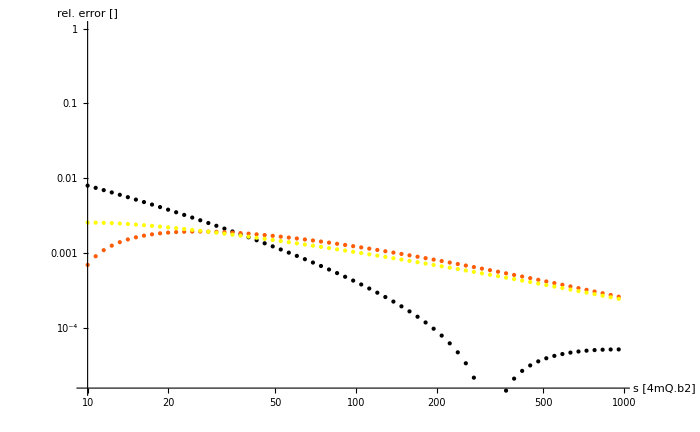

```mathematica
Show[getDiffStrictHELimit[1,{1,2,3}],ImageSize-> 700]
```

A: if one takes, the physically better expansion (NB: I still don’t know, whether this makes sense), i.e. to cut ln(Δ) to ln(N)^2 (as the coefficients below are NOT determined correct) the convergence gets worse, as the full resummation contains these unsatisfied elements

So the overall answer is:
- in the region where we trust resummation, i.e. threshold region, it DOES NOT converge
- and in the region where we don’t trust resummation, i.e. HE region, it DOES converge

### Case 3: Can we give a point that splits threshold- and HE-limit

```mathematica
(*getLinearEnvelope[data_List]:=Module[{xs,ys,m,c,max,posMax,xMax,ms,posM},
(* seperate *)
{xs,ys} = Transpose[data];
(* find maximum *)
max =Max@ys;
posMax=First@First@Position[ys,max];
xMax = xs[[posMax]];
c=max;
(* minimize m *)
ms=(d↦(d[[2]]-c)/(d[[1]]-xMax))/@Delete[data,posMax];
m=Min@Abs@ms;
posM=First@First@Position[Abs@ms,m];
(*x↦ms[[posM]]*(x-xMax)+c*)
{ms[[posM]],xMax,c}
];*)
getLinearEnvelope[data_List]:=Module[{xs,ys,f,m,c,diff,sol},
(* seperate *)
{xs,ys} = Transpose[data];
f = x↦m*x+c;
diff=Table[f[d[[1]]]-d[[2]],{d,data}];
sol=FindFit[data,{f[x],Min[diff] ≥ 0},{m,c},x];
{m,c}/.sol
];
(*Module[{data,env},
data = {{-1.5,1.036651405734735},{-1.49,1.035614827292849},{-1.48,1.0344464645201525},{-1.47,1.0331455709782573},{-1.46,1.0317114322992587},{-1.45,1.0301433674009997},{-1.44,1.0284407297190623},{-1.43,1.0266029084547774},{-1.42,1.0246293298385085},{-1.41,1.0225194584074127},{-1.4,1.0202727982967783},{-1.39,1.017888894543983},{-1.38,1.0153673344040373},{-1.37,1.0127077486794553},{-1.3599999999999999,1.0099098130397022},{-1.35,1.0069732493886125},{-1.34,1.0038978271977674},{-1.33,1.0006833648656066},{-1.32,0.9973297310758867},{-1.31,0.9938368461580375},{-1.3,0.9902046834476083},{-1.29,0.9864332706449636},{-1.28,0.9825226911702591},{-1.27,0.9784730855125623},{-1.26,0.9742846525710335},{-1.25,0.9699576509857337},{-1.24,0.965492400455801},{-1.23,0.9608892830423358},{-1.22,0.9561487444528611},{-1.21,0.9512712953080676},{-1.2,0.9462575123795979},{-1.19,0.9411080398067643},{-1.18,0.9358235902811946},{-1.17,0.9304049461996808},{-1.16,0.924852960779482},{-1.15,0.9191685591375981},{-1.1400000000000001,0.9133527393240743},{-1.13,0.907406573310592},{-1.12,0.9013312079288086},{-1.1099999999999999,0.895127865755023},{-1.1,0.8887978459373922},{-1.0899999999999999,0.8823425249618233},{-1.08,0.875763357352649},{-1.07,0.8690618763041126},{-1.06,0.8622396942386777},{-1.05,0.8552985032881265},{-1.04,0.8482400756934283},{-1.03,0.8410662641197745},{-1.02,0.8337790018800886},{-1.01,0.8263803030696608},{-1.,0.818872262599097},{-0.99,0.8112570561282957},{-0.98,0.8035369398949772},{-0.97,0.795714250434471},{-0.96,0.7877914041870889},{-0.95,0.7797708969895925},{-0.94,0.7716553034473794},{-0.9299999999999999,0.7634472761841726},{-0.92,0.7551495449657585},{-0.91,0.7467649156973433},{-0.9,0.7382962692860162},{-0.89,0.7297465603737505},{-0.88,0.7211188159329966},{-0.87,0.7124161337253702},{-0.86,0.703641680621504},{-0.85,0.694798690780851},{-0.84,0.6858904636903511},{-0.83,0.6769203620627978},{-0.82,0.667891809591216},{-0.8099999999999999,0.6588082885642639},{-0.7999999999999999,0.649673337340301},{-0.79,0.6404905476807814},{-0.78,0.6312635619468412},{-0.77,0.6219960701590571},{-0.76,0.6126918069235823},{-0.75,0.6033545482273832},{-0.74,0.5939881081059191},{-0.73,0.5845963351869471},{-0.72,0.5751831091157231},{-0.71,0.5657523368638978},{-0.7,0.5563079489307078},{-0.69,0.5468538954396939},{-0.6799999999999999,0.5373941421382006},{-0.6699999999999999,0.5279326663060973},{-0.66,0.5184734525809228},{-0.65,0.5090204887070093},{-0.64,0.49957776121656156},{-0.63,0.4901492510512314},{-0.62,0.48073892913223165},{-0.61,0.4713507518898898},{-0.6,0.4619886567599183},{-0.59,0.45265655765774854},{-0.58,0.44335834048243283},{-0.57,0.4340978584018753},{-0.5599999999999999,0.4248789275636796},{-0.5499999999999999,0.4157053225174383},{-0.54,0.4065807715874325},{-0.53,0.3975089525659821},{-0.52,0.388493488270524},{-0.51,0.37953794227534854},{-0.5,0.37064581459457974},{-0.49,0.3618205375381691},{-0.48,0.3530654716374849},{-0.47000000000000003,0.34438390167838834},{-0.45999999999999996,0.3357790328505139},{-0.45,0.3272539870246241},{-0.4399999999999999,0.3188117991633469},{-0.42999999999999994,0.3104554138808144},{-0.41999999999999993,0.3021876821557794},{-0.4099999999999999,0.294011358208641},{-0.3999999999999999,0.28592909655032245},{-0.3899999999999999,0.27794344921065745},{-0.3799999999999999,0.2700568631534715},{-0.3699999999999999,0.2622716778849145},{-0.3599999999999999,0.25459012326106556},{-0.34999999999999987,0.24701431750016967},{-0.3400000000000001,0.23954626540420515},{-0.33000000000000007,0.23218785679387025},{-0.32000000000000006,0.22494086516031983},{-0.31000000000000005,0.2178069465363334},{-0.30000000000000004,0.21078763858875943},{-0.29000000000000004,0.20388435993362655},{-0.28,0.1970984096742539},{-0.2700000000000001,0.19043096716222815},{-0.26,0.18388309198013802},{-0.25,0.17745572414456295},{-0.24,0.17114968452673668},{-0.22999999999999995,0.16496567548797603},{-0.21999999999999997,0.15890428172590862},{-0.21,0.15296597132721446},{-0.19999999999999993,0.14715109702178386},{-0.18999999999999992,0.14145989763264574},{-0.17999999999999994,0.1358924997150827},{-0.1699999999999999,0.1304489193795292},{-0.1599999999999999,0.12512906428845408},{-0.14999999999999994,0.11993273582201243},{-0.1399999999999999,0.11485963140354122},{-0.1299999999999999,0.10990934697468288},{-0.11999999999999987,0.10508137961426277},{-0.10999999999999988,0.1003751302893483},{-0.09999999999999988,0.09578990672999776},{-0.0900000000000001,0.09132492641769233},{-0.08000000000000007,0.08697931967797161},{-0.07000000000000008,0.08275213286634442},{-0.060000000000000026,0.07864233163964558},{-0.05000000000000004,0.0746488042996459},{-0.04000000000000004,0.07077036519953173},{-0.030000000000000016,0.067005758206883},{-0.020000000000000028,0.06335366020718705},{-0.010000000000000005,0.05981268464203833},{0.,0.05638138507115444},{0.009999999999999986,0.05305825880338524},{0.02000000000000003,0.04984175027089914},{0.03,0.04673025488553961},{0.04000000000000003,0.04372212244802724},{0.05000000000000005,0.0408156607211918},{0.060000000000000026,0.038009138942689945},{0.07000000000000008,0.03530079130024088},{0.0800000000000001,0.032688820362305145},{0.09000000000000011,0.030171400457277137},{0.1000000000000001,0.02774668099492005},{0.1100000000000001,0.025412789723669456},{0.12000000000000012,0.023167835918217906},{0.13000000000000012,0.02100991349175529},{0.14000000000000012,0.0189371040279054},{0.15000000000000016,0.016947479727594257},{0.16000000000000011,0.015039106266768106},{0.16999999999999993,0.013210045561176043},{0.17999999999999994,0.011458358435271968},{0.18999999999999997,0.009782107192184473},{0.19999999999999998,0.008179358083117807},{0.20999999999999994,0.006648183674105905},{0.21999999999999995,0.005186665108865008},{0.23,0.003792894266844637},{0.23999999999999996,0.0024649758156030334},{0.25,0.001201029157220937},{0.26,8.097314955955858*^-7},{0.27,0.0011423865647991198},{0.28,0.0022255271193141937},{0.29000000000000004,0.0032520357101295913},{0.30000000000000004,0.004223693770474247},{0.31000000000000005,0.005142258533538222},{0.32,0.006009461814739704},{0.3300000000000001,0.006827008892380691},{0.3400000000000001,0.007596577484640438},{0.35000000000000003,0.00831981682052408},{0.3600000000000001,0.008998346802306297},{0.37000000000000016,0.009633757257054683},{0.3800000000000001,0.010227607274496146},{0.3900000000000001,0.010781424628643595},{0.40000000000000013,0.011296705280165232},{0.4100000000000002,0.011774912956806386},{0.4199999999999999,0.012217478808659851},{0.4299999999999999,0.012625801135208144},{0.43999999999999995,0.013001245181048964},{0.45,0.013345142997031996},{0.4599999999999999,0.013658793363656701},{0.47,0.013943461773623121},{0.48,0.014200380470299059},{0.49,0.014430748539169275},{0.5,0.014635732049145513},{0.5100000000000002,0.014816464240747049},{0.52,0.014974045758217112},{0.5300000000000002,0.01510954492265015},{0.54,0.0152239980432258},{0.5499999999999998,0.015318409763774262},{0.56,0.015393753441894571},{0.5699999999999998,0.015450971558003169},{0.5800000000000001,0.01549097615168559},{0.5899999999999999,0.015514649282983566},{0.6000000000000001,0.015522843516171133},{0.6099999999999999,0.015516382423687226},{0.6200000000000001,0.015496061108209476},{0.6299999999999999,0.015462646740493613},{0.6400000000000001,0.015416879111252897},{0.6499999999999999,0.015359471194815297},{0.6600000000000001,0.015291109723058976},{0.6699999999999999,0.015212455767506301},{0.6800000000000002,0.015124145328250472},{0.69,0.01502678992787098},{0.7000000000000002,0.01492097720914495},{0.71,0.014807271534814334},{0.7200000000000002,0.014686214588574623},{0.73,0.014558325975520942},{0.7400000000000002,0.014424103821434124},{0.75,0.014284025369442255},{0.7600000000000002,0.01413854757331458},{0.77,0.013988107686354945},{0.7800000000000002,0.013833123845113007},{0.79,0.01367399564707172},{0.8000000000000003,0.013511104721633171},{0.81,0.013344815293880471},{0.8199999999999998,0.013175474740388405},{0.8300000000000001,0.013003414136548555},{0.8399999999999999,0.012828948795009912},{0.8500000000000001,0.01265237879490314},{0.8599999999999999,0.01247398950122821},{0.8700000000000001,0.012294052074451722},{0.8799999999999999,0.012112823969490929},{0.8900000000000001,0.011930549424582567},{0.8999999999999999,0.011747459939093013},{0.9100000000000001,0.011563774740743531},{0.9199999999999999,0.011379701241658208},{0.9300000000000002,0.011195435483331493},{0.94,0.011011162570712323},{0.9500000000000002,0.010827057094781586},{0.96,0.010643283544237764},{0.9700000000000002,0.010459996705882891},{0.98,0.010277342053852534},{0.9900000000000002,0.010095456128001787},{1.,0.009914466901218454},{1.0100000000000002,0.009734494135688013},{1.02,0.009555649728684792},{1.0300000000000002,0.009378038047841689},{1.04,0.009201756255237113},{1.0500000000000003,0.009026894622079576},{1.06,0.008853536832605365},{1.0699999999999998,0.00868176027821875},{1.08,0.008511636341676284},{1.0899999999999999,0.008343230671867154},{1.1,0.0081766034488405},{1.1099999999999999,0.00801180963984819},{1.12,0.007848899246303536},{1.13,0.007687917541853136},{1.1400000000000001,0.007528905301771682},{1.15,0.007371899024105443},{1.1600000000000001,0.007216931142605345},{1.17,0.007064030231171983},{1.1800000000000002,0.006913221201443753},{1.19,0.006764525492167664},{1.2000000000000002,0.006617961251102324},{1.21,0.006473543510150072},{1.2200000000000002,0.006331284353419913},{1.23,0.006191193078572257},{1.2400000000000002,0.006053276351651807},{1.25,0.005917538355011349},{1.2600000000000002,0.0057839809307094255},{1.27,0.0056526037154682515},{1.2800000000000002,0.0055234042727783485},{1.29,0.005396378216637055},{1.3000000000000003,0.005271519331710465},{1.31,0.005148819688381303},{1.3199999999999998,0.005028269751630967},{1.33,0.00490985848555157},{1.3399999999999999,0.004793573453541735},{1.35,0.004679400913481466},{1.3599999999999999,0.004567325910120541},{1.37,0.004457332359602006},{1.38,0.0043494031348289735},{1.3900000000000001,0.004243520142056569},{1.4,0.004139664399238413},{1.4100000000000001,0.004037816103706064},{1.42,0.0039379547048896376},{1.4300000000000002,0.0038400589631616476},{1.44,0.0037441070188216114},{1.4500000000000002,0.00365007644613244},{1.46,0.0035579443073606143},{1.4700000000000002,0.0034676872108837897},{1.48,0.0033792813575607233},{1.4900000000000002,0.003292702588721849},{1.5,0.0032079264317070454}};
data=(d↦{d[[1]],Log10@d[[2]]})/@data;
env=getLinearEnvelope@data;
Print@env;
Show[{ListPlot[data],Plot[env[[1]]*x+env[[2]],{x,-1.5,1.5}]}]
]*)
```

```mathematica
(* @param v σ ~ β^v <-> Beta[n,v/2+1] *)
(* @param orders At which orders should the expansion be checked? *)
getSplitLimits[v_,orders_]:=Module[{
fullN,serΔLLMax,serΔLLs,serNs,fullρ,serρs,
ηs,lFull,lSer,toηPlot, lRelErrs, envs, y
},
(* get series *)
serΔLLMax = Normal@Series[ΔLL,{lnN,0,Max@orders}];
serΔLLs =Table[Normal@Series[serΔLLMax,{lnN,0,o}],{o,orders}];
(* build functions *)
fullN = n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]})];
serNs =(s↦ (n↦Evaluate[Beta[n,v/2+1]*(s/.{lnN -> Log[n+1]})]))/@serΔLLs;
(* compute inverse *)
fullρ = getInvMellinTrafo[fullN//.toN[]];
serρs=(f↦getInvMellinTrafo[f//.toN[]])/@serNs;
(* compute values on grid *)
ηs = Table[10^j,{j,-1.5,1.5,.01}];
lFull = Parallelize@Table[fullρ[η2ρ@η],{η,ηs}];
lSer = (fρ↦Parallelize@Table[fρ[η2ρ@η],{η,ηs}])/@serρs;
(* relative error *)
lRelErrs = Parallelize[(l↦Log10@Abs[(Re@l-Re@lFull)/Re@lFull])/@lSer];
(* compute envelopes *)
toηPlot[l_]:=Transpose[{Log10@ηs,l}];
envs = Parallelize[(l↦getLinearEnvelope[toηPlot@l])/@lRelErrs];
(* Plot *)
GraphicsRow[{
Show[{
ListPlot[(l↦toηPlot@l)/@lRelErrs,AxesLabel-> {"ln10(η) []","log10 rel. error []"},PlotStyle->ColorData[3,"ColorList"]],
Plot[Evaluate[(env↦env[[1]]*ln10η+env[[2]])/@envs],{ln10η,Min@Log10@ηs,Max@Log10@ηs},PlotStyle->ColorData[3,"ColorList"]]
}],
Plot[Evaluate[(env↦env[[1]]*ln10η+env[[2]])/@envs],{ln10η,Min@Log10@ηs,Max@Log10@ηs},AxesLabel-> {"ln10(η) []","log10 rel. error []"},PlotStyle->ColorData[3,"ColorList"]]
}]
(*y=-1;
GraphicsRow[{
Plot[Evaluate@Parallelize[(env↦env[[1]]*ln10η+env[[2]])/@envs],{ln10η,Min@Log10@ηs,Max@Log10@ηs},AxesLabel-> {"ln10(η) []","log10 rel. error []"},PlotStyle->ColorData[3,"ColorList"]],
ListPlot[Evaluate@Parallelize[(e↦{e[[1]],e[[2]][[1]]})/@Transpose[{orders,envs}]],AxesLabel-> {"order", "m"}],
ListPlot[Evaluate@Parallelize[(e↦{e[[1]],e[[2]][[2]]})/@Transpose[{orders,envs}]],AxesLabel-> {"order", "c"}],
ListPlot[Evaluate@Parallelize[(e↦{e[[1]],(y-e[[2]][[2]])/e[[2]][[1]]})/@Transpose[{orders,envs}]],AxesLabel-> {"order", "y=-1"}]
},Spacings->0]*)
];
```

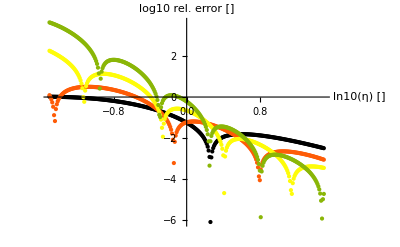

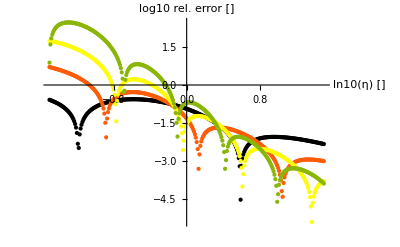

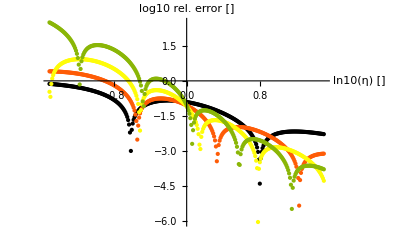

```mathematica
Do[Print@Show[getSplitLimits[v,{2,6,10,14}],ImageSize->1500],{v,{1,2,3}}]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {9.1184×10^-7, 5.45679×10^-6, 3.96634×10^-14}, is returned.

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.32363×10^-10, 0.0000139124, 4.27836×10^-15}, is returned.

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {2.11206×10^-9, 0.000173423, 1.24604×10^-14}, is returned.

General::stop: Further output of FindFit :: eit will be suppressed during this calculation.

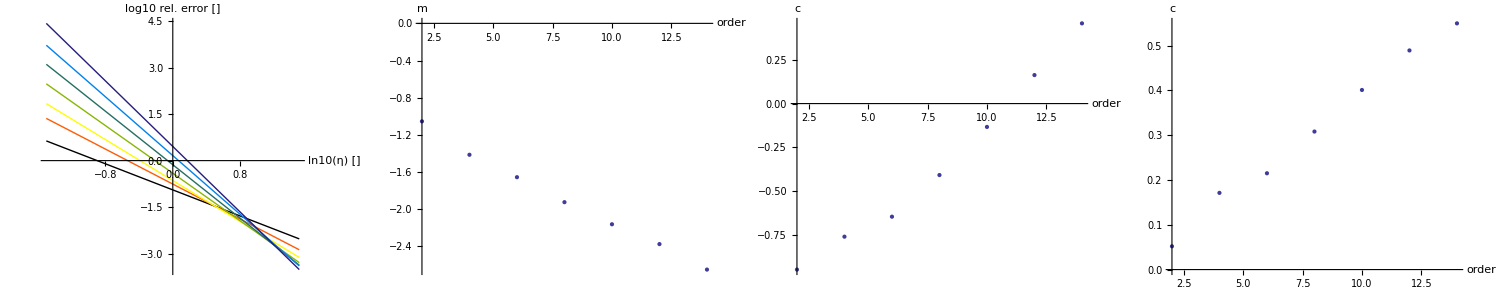

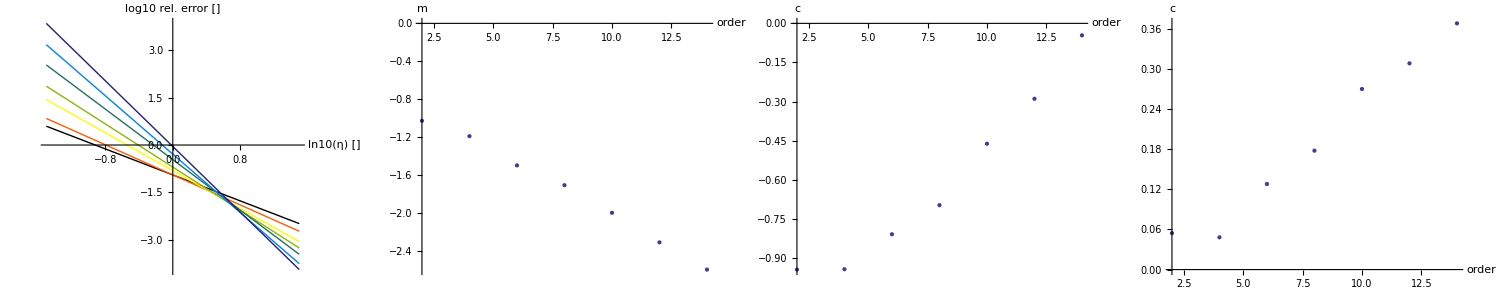

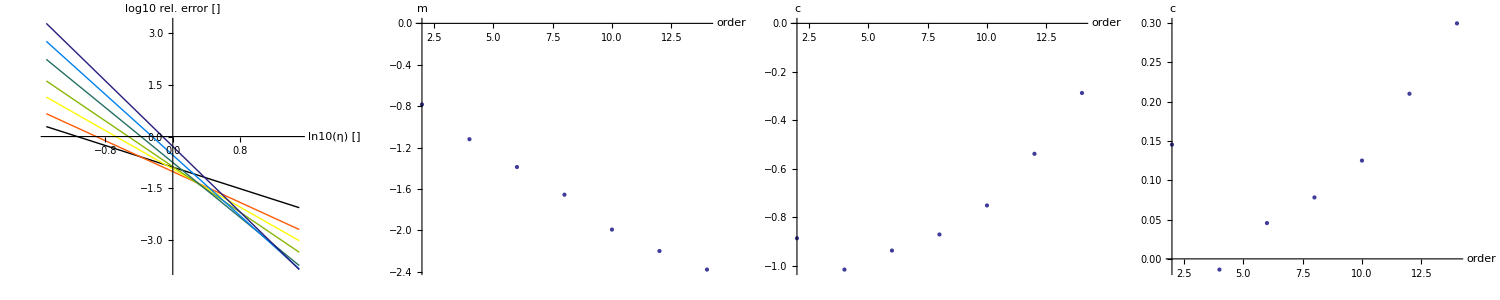

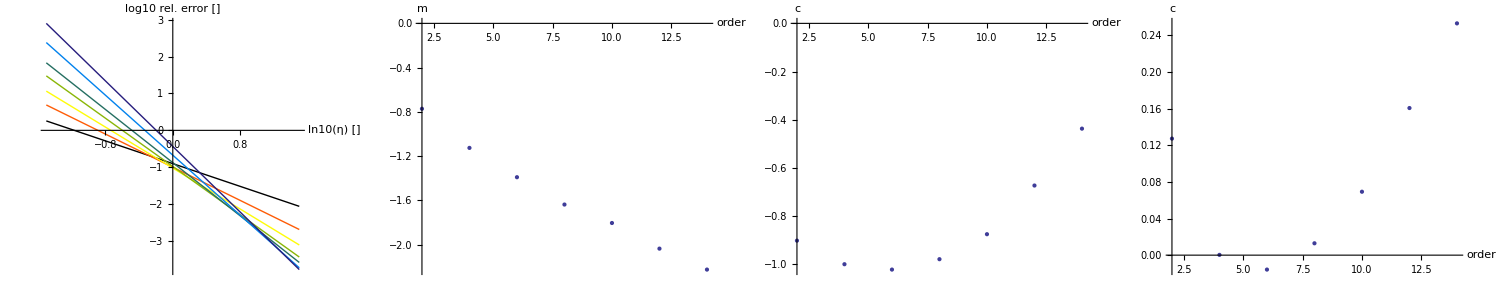

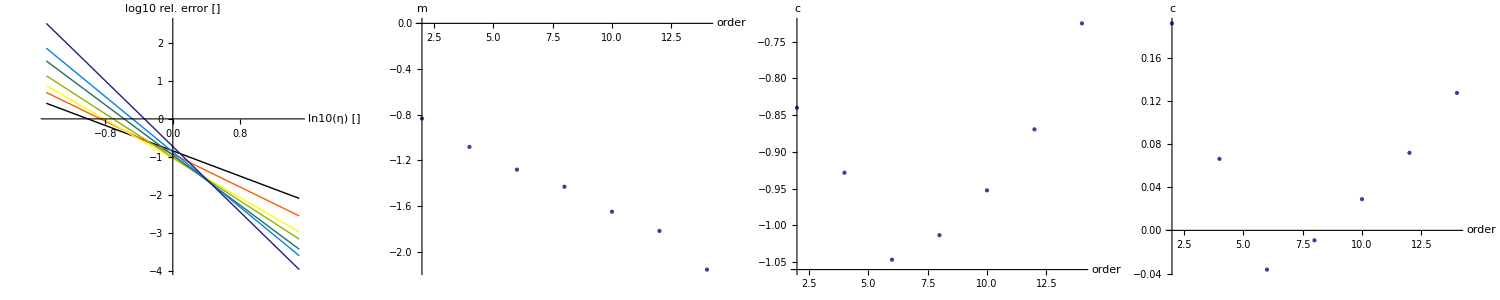

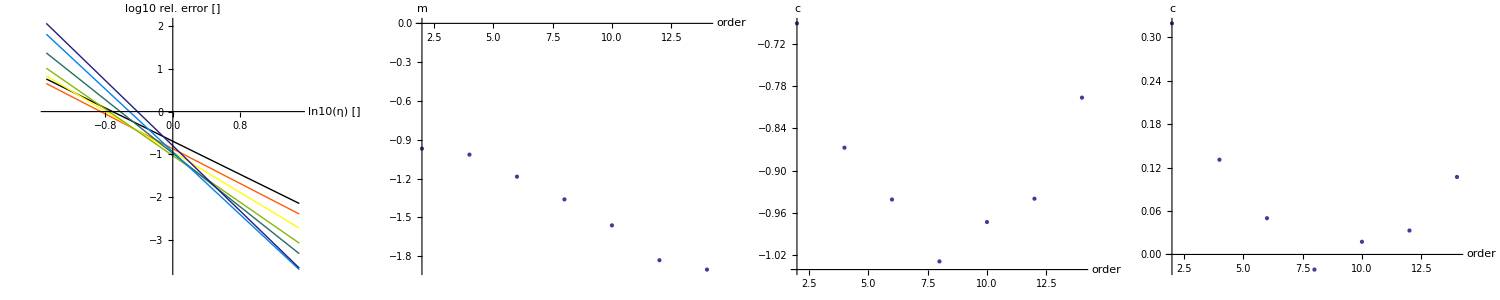

```mathematica
Do[Print@Show[getSplitLimits[v,{2,4,6,8,10,12,14}],ImageSize->1500],{v,{0,1,2,3,5,7}}]
```